```mathematica
J0 = {{-sigma, sigma, 0}, {r-z,-1, -x},{y,x,-b}};
{{-sigma,sigma,0},{r-z,-1,-x},{y,x,-b}};
J = J0/.{sigma ->  10, b ->8/3, r  ->28};
eigens = Eigenvalues[J];

eigens1 = eigens/.{x ->0, y->0, z->0};
AnyTrue[{Re[Evaluate[eigens1[[1]]]],Re[Evaluate[eigens1[[2]]]],Re[Evaluate[eigens1[[3]]]]}, LessThan[0]]

eigens2 = eigens/.{x ->-sqrt(6)/2, y->-sqrt(6)/2, z->27};
AnyTrue[{Re[Evaluate[eigens1[[1]]]],Re[Evaluate[eigens1[[2]]]],Re[Evaluate[eigens1[[3]]]]}, LessThan[0]]

eigens2 = eigens/.{x ->sqrt(6)/2, y->sqrt(6)/2, z->27};
AnyTrue[{Re[Evaluate[eigens1[[1]]]],Re[Evaluate[eigens1[[2]]]],Re[Evaluate[eigens1[[3]]]]}, LessThan[0]]

Tr[J0]
```

True

True

True

-1-b-sigma

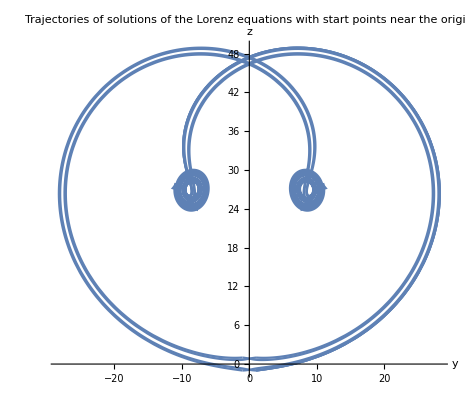

```mathematica
ClearAll["Global`*"]
sigma0 = 10; 
b0 = 8/3;
r0=28;
tMax = 4;

sol[u_, v_, w_]:= NDSolve[{x'[t] == sigma0*(y[t]-x[t]), 
y'[t] == r0*x[t]-y[t]-x[t]*z[t], 
z'[t] == x[t]*y[t] - b0*z[t],
x[0] ==u,
y[0] ==v,
z[0] ==w},
{x,y,z}, 
{t, 0, tMax}];

TableFinal = {{-1,-1,-1}, {-1,-1,1}, {-1,1,1}, {-1,1,-1}, {1,1,-1}, {1,-1,-1}, {1,-1,1}, {1,1,1}, {1,1,-1}, {1,1,-1}};

title = "Trajectories of solutions of the Lorenz equations with start points near the origin";
Show[Table[ParametricPlot[Evaluate[{y[t],z[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]],TableFinal[[i,3]]]], {t,0,tMax},PlotRange->All,AxesLabel -> {y,z},PlotLabel->Style[title,FontSize->12]]/.Line[x_]:>{Arrowheads[{0, 0.03, 0, 0}],Arrow[x]}, {i,Length[TableFinal]}]]
```

```mathematica
TableFinal
```

{{-1,-1.},{-1,-0.9},{-1,-0.8},{-1,-0.7},{-1,-0.6},{-1,-0.5},{-1,-0.4},{-1,-0.3},{-1,-0.2},{-1,-0.1},{-1,0.},{-1,0.1},{-1,0.2},{-1,0.3},{-1,0.4},{-1,0.5},{-1,0.6},{-1,0.7},{-1,0.8},{-1,0.9},{-1,1.},{-1.,1},{-0.9,1},{-0.8,1},{-0.7,1},{-0.6,1},{-0.5,1},{-0.4,1},{-0.3,1},{-0.2,1},{-0.1,1},{0.,1},{0.1,1},{0.2,1},{0.3,1},{0.4,1},{0.5,1},{0.6,1},{0.7,1},{0.8,1},{0.9,1},{1.,1},{1,-1.},{1,-0.9},{1,-0.8},{1,-0.7},{1,-0.6},{1,-0.5},{1,-0.4},{1,-0.3},{1,-0.2},{1,-0.1},{1,0.},{1,0.1},{1,0.2},{1,0.3},{1,0.4},{1,0.5},{1,0.6},{1,0.7},{1,0.8},{1,0.9},{1,1.},{-1.,-1},{-0.9,-1},{-0.8,-1},{-0.7,-1},{-0.6,-1},{-0.5,-1},{-0.4,-1},{-0.3,-1},{-0.2,-1},{-0.1,-1},{0.,-1},{0.1,-1},{0.2,-1},{0.3,-1},{0.4,-1},{0.5,-1},{0.6,-1},{0.7,-1},{0.8,-1},{0.9,-1},{1.,-1}}